# Why not Galerkin here?

```mathematica
a=0;
b=3;
H[fx_]:=∫_a^b fxⅆx;
ϕ1=x;
ϕ2=x^2;
ϕ3=x^3;
f=x^3 ⅇ^x;
A={
{H[ϕ1 D[ϕ1, x]],H[ϕ1 D[ϕ2, x]],H[ϕ1 D[ϕ3, x]]},
{H[ϕ2 D[ϕ1, x]],H[ϕ2 D[ϕ2, x]],H[ϕ2 D[ϕ3, x]]},
{H[ϕ3 D[ϕ1, x]],H[ϕ3 D[ϕ2, x]],H[ϕ3 D[ϕ3, x]]}
}//FullSimplify;
b={H[ϕ1 f], H[ϕ2 f],H[ϕ3 f]}//FullSimplify;
{a1,a2,a3}=Dot[Inverse[A],b]//FullSimplify;
A
b
a1
a2
a3
```

{{9/2,18,243/4},{9,81/2,729/5},{81/4,486/5,729/2}}

{-24+33 ⅇ^3,120+78 ⅇ^3,9 (-80+29 ⅇ^3)}

4/3 (-2144+113 ⅇ^3)

20 (92-5 ⅇ^3)

20/81 (-1352+77 ⅇ^3)

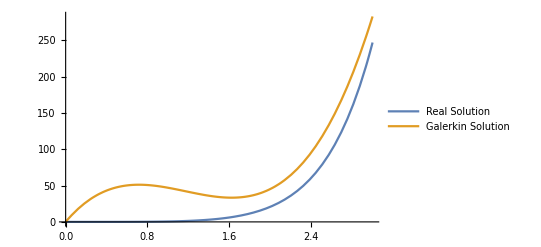

```mathematica
yy=a1 x+a2 x^2+a3 x^3;
y=∫_0^x t^3 ⅇ^t ⅆt//FullSimplify;
Plot[{y,yy},{x,0,3},PlotLegends->{"Real Solution","Galerkin Solution"}]
```

# When we talk about Hermite...

```mathematica
Clear["Global`*"];
A={
{1,xk,xk^2,xk^3},
{0,1,2xk,3 xk^2},
{1,xk1,xk1^2,xk1^3},
{0,1,2xk1,3 xk1^2}
};
b={uk,uki,uk1,uk1i};
ϕ=Dot[{1,x,x^2,x^3},Inverse[A]]//FullSimplify;
Φ=ϕ/.{xk1->(xk+hk)}//FullSimplify;
ψ=Φ/.{x->(hk ξ+xk)}//FullSimplify;
ϕ
Φ
ψ
```

{-((x-xk1)^2 (2 x-3 xk+xk1))/(xk-xk1)^3,((x-xk) (x-xk1)^2)/(xk-xk1)^2,((x-xk)^2 (2 x+xk-3 xk1))/(xk-xk1)^3,((x-xk)^2 (x-xk1))/(xk-xk1)^2}

{((hk+2 x-2 xk) (hk-x+xk)^2)/hk^3,((x-xk) (hk-x+xk)^2)/hk^2,((x-xk)^2 (3 hk-2 x+2 xk))/hk^3,-((x-xk)^2 (hk-x+xk))/hk^2}

{(-1+ξ)^2 (1+2 ξ),hk (-1+ξ)^2 ξ,(3-2 ξ) ξ^2,hk (-1+ξ) ξ^2}

```mathematica
ψ//Expand
```

{1-3 ξ^2+2 ξ^3,hk ξ-2 hk ξ^2+hk ξ^3,3 ξ^2-2 ξ^3,-hk ξ^2+hk ξ^3}